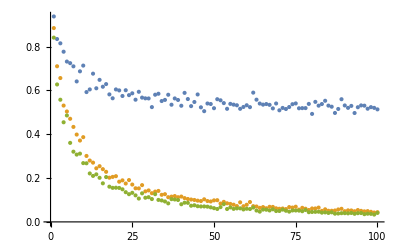

```mathematica
ListPlot[{Table[With[{p1=RandomVariate[GammaDistribution[1,b],1000],p2=RandomVariate[GammaDistribution[1,b],1000]},
CosineDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p2]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[1,b],1000],p2=RandomVariate[GammaDistribution[1,b],1000]},
CosineDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p1]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[1,b],1000],p2=RandomVariate[GammaDistribution[1,b],1000]},
CosineDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[2#]]&,p1]]
]//N,{b,0.1,10,0.1}]
}]
```

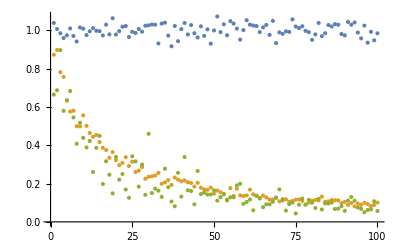

```mathematica
ListPlot[{Table[With[{p1=RandomVariate[GammaDistribution[1,b],1000],p2=RandomVariate[GammaDistribution[1,b],1000]},
CorrelationDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p2]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[1,b],1000],p2=RandomVariate[GammaDistribution[1,b],1000]},
CorrelationDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p1]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[1,b],50],p2=RandomVariate[GammaDistribution[1,b],50]},
CorrelationDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[2#]]&,p1]]
]//N,{b,0.1,10,0.1}]
}]
```

```mathematica
Expectation[(u x + v y+w z)/((x+y+z)*(u+v+w)), {u \[Distributed]PoissonDistribution[x], v\[Distributed]PoissonDistribution[y],w\[Distributed]PoissonDistribution[z]}]
```

$Aborted

```mathematica
Expectation[(u x + v y)/(Sqrt[x^2+y^2]*Sqrt[u^2+v^2]), {u \[Distributed]PoissonDistribution[x], v\[Distributed]PoissonDistribution[y]}]
```

$Aborted

```mathematica
Expectation[CosineDistance[{x,y},{u,v}],{x \[Distributed]PoissonDistribution[Mean[{x,u}]],y \[Distributed]PoissonDistribution[Mean[{y,v}]],u \[Distributed]PoissonDistribution[Mean[{x,u}]],v \[Distributed]PoissonDistribution[Mean[{y,v}]]}]
```

Expectation[1-(u x+v y)/(√(Abs[u]^2+Abs[v]^2) √(Abs[x]^2+Abs[y]^2)),{x\[Distributed]PoissonDistribution[(u+x)/2],y\[Distributed]PoissonDistribution[(v+y)/2],u\[Distributed]PoissonDistribution[(u+x)/2],v\[Distributed]PoissonDistribution[(v+y)/2]}]

```mathematica
Sqrt[x^2+y^2]*Sqrt[u^2+v^2]//FullSimplify
```

√(u^2+v^2) √(x^2+y^2)

```mathematica
Expectation[Sqrt[(x^2+y^2)]Sqrt[(u^2+v^2)], {u \[Distributed]PoissonDistribution[x], v\[Distributed]PoissonDistribution[y]}]
```

```mathematica
Expectation[u^2+v^2+w^2,{u\[Distributed]PoissonDistribution[x],v\[Distributed]PoissonDistribution[y],w\[Distributed]PoissonDistribution[z]}]
```

x+x^2+y+y^2+z+z^2

```mathematica
ExpectedCosineDistance[x_List]:=2-2Total[x^2]/((Sqrt[Total[x]+Total[x^2]])*Norm[x])
```

```mathematica
2-2Sum[Subscript[x, i]^2,i]/((Sqrt[Sum[Subscript[x, i]+Subscript[x, i]^2,i]])*Norm[x])//FullSimplify//TraditionalForm
```

2-(2 ∑_i x_i^2)/(Norm[x] √(∑_i (x_i^2+x_i)))

```mathematica
ExpectedCorrelationDistance[y_List]:=With[{x=y-Mean[y]},2-2Total[x^2]/((Sqrt[Total[x]+Total[x^2]])*Norm[x])]
```

```mathematica
ExpectedCosineDistance[{1,5,0.1,0.1,2,3,5,11}]//N
```

0.066281

```mathematica
Table[CosineDistance[{1,5,0.1,0.1,2,3,5,11},Map[RandomVariate[PoissonDistribution[#]]&,{1,5,0.1,0.1,2,3,5,11}]]//N,{100}]//Mean
```

0.0470611

```mathematica
CosineDistance[{x,y},{u,v}]
```

1-(u x+v y)/(√(Abs[u]^2+Abs[v]^2) √(Abs[x]^2+Abs[y]^2))

```mathematica
{1,2,3}^2
```

{1,4,9}

```mathematica
CosineDistance[{0,0,0},{0,0,0}]
```

0

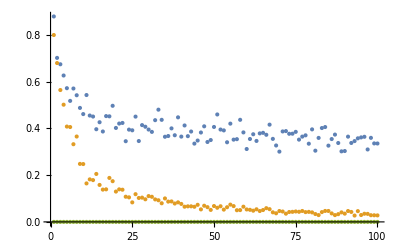

```mathematica
ListPlot[{Table[With[{p1=RandomVariate[GammaDistribution[2,b],200],p2=RandomVariate[GammaDistribution[2,b],200]},
CosineDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p2]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[2,b],200]},
CosineDistance[Map[RandomVariate[PoissonDistribution[#]]&,p1],Map[RandomVariate[PoissonDistribution[#]]&,p1]]
]//N,{b,0.1,10,0.1}],
Table[With[{p1=RandomVariate[GammaDistribution[2,b],200]},
With[{p2=Map[RandomVariate[PoissonDistribution[#]]&,p1]},
ExpectedCorrelationDistance[p1]]
]//N,{b,0.1,10,0.1}]
}]
```

```mathematica
With[{
p1=RandomVariate[GammaDistribution[2,4],500]
},
With[{
data = Map[RandomVariate[PoissonDistribution[#],500]&,p1]
},
Variance[Sqrt[data][[1]]]//N
]
]
```

0.26851

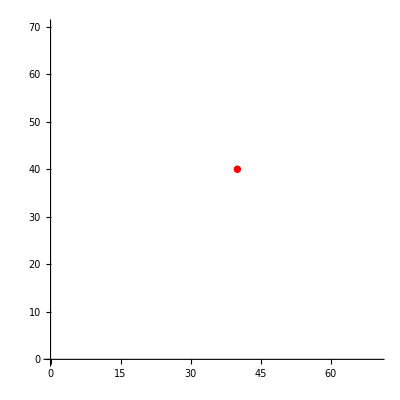

```mathematica
ListPlot[{{40,40}},AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{0,70},{0,70}},PlotStyle->Red]
```

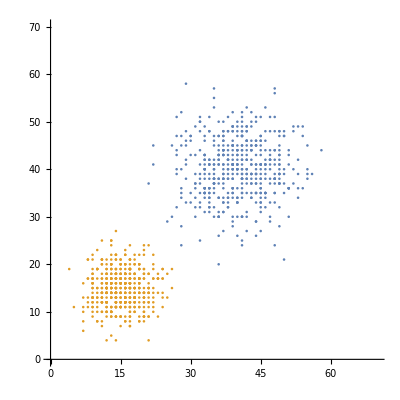

```mathematica
ListPlot[{
RandomVariate[PoissonDistribution[40],{500,2}],
RandomVariate[PoissonDistribution[15],{500,2}]},AspectRatio->1,PlotRange->{{0,70},{0,70}},AxesOrigin->{0,0}]
```